In this analysis, we set everything in terms of the predator body size
Prey body size is then determined as a function of the predator body size: OptPreyMass = f[PredMass]

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqnP = (w*bPred*P*C +(1-w)* bPredSub*Sub*P) - μPred*P/.{bPred->bPred[Mp],bPredSub->bPredSub[Mp],μPred->μPred[Mp]}; 
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+w*bmort*P)*C/.{k->kRes,λ->λ[Mp],μ->μ[Mp],σ->σ[Mp],bmort->bmort[Mp]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R)))*C/.{k->kRes,λ->λ[Mp],Y->Y[Mp]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC,0==eqnR},{P,C,R}]];
```

```mathematica
Length[LVSS]
```

7

```mathematica
Psol = P/.LVSS[[5]]
Csol = C/.LVSS[[5]]
Rsol = R/.LVSS[[5]]
```

((8 λ[Mp])/w-(8 μ[Mp])/w+((-3 √kRes √w √α √bPred[Mp] √Y[Mp]+√(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp]))) (kRes w α bPred[Mp] Y[Mp]+2 (Sub (-1+w) bPredSub[Mp]+μPred[Mp]) σ[Mp]))/(√kRes w^(3/2) √α √bPred[Mp] √Y[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(8 bmort[Mp])

(Sub (-1+w) bPredSub[Mp]+μPred[Mp])/(w bPred[Mp])

kRes/4+(√kRes √(9 kRes w α bPred[Mp] Y[Mp]-16 λ[Mp] (Sub (-1+w) bPredSub[Mp]+μPred[Mp])))/(4 √w √α √bPred[Mp] √Y[Mp])

```mathematica
PsolNoSubsidies= Psol/.w->1
CsolNoSubsidies= Csol/.w->1
```

(8 λ[Mp]-8 μ[Mp]+((-3 √kRes √α √bPred[Mp] √Y[Mp]+√(9 kRes α bPred[Mp] Y[Mp]-16 λ[Mp] μPred[Mp])) (kRes α bPred[Mp] Y[Mp]+2 μPred[Mp] σ[Mp]))/(√kRes √α √bPred[Mp] √Y[Mp] μPred[Mp]))/(8 bmort[Mp])

μPred[Mp]/bPred[Mp]

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C],D[eqnP,R]},
{D[eqnC,P],D[eqnC,C],D[eqnC,R]},
{D[eqnR,P],D[eqnR,C],D[eqnR,R]}})/.{P->Psol,C->Csol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/data/carnivoredensities_trimmed.csv"}],"csv"];
```

***Declare Metabolic Parameters***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/src/metabolic_constants.nb"}]];
```

***Declare Allometric Functions - SPECIFIC TO MODEL AND PERSPECTIVE***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/src/allometric_functions_predpersp.nb"}]];
```

***Declare PPMR***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/src/ppmr_primary.nb"}]];
```

***Declare Analysis Functions***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/src/analysis_functions.nb"}]];
```

Show the inputted PPMR

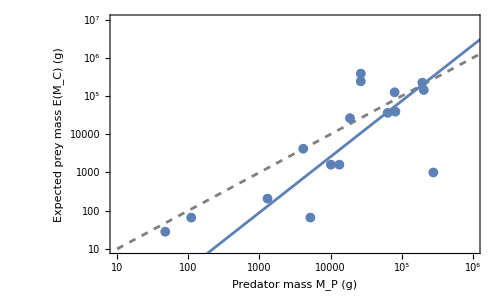

```mathematica
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotLM = Show[{
ListLogLogPlot[ExpPreymassdata*1000,Frame->True,FrameLabel->{"Predator mass M_P (g)","Expected prey mass E(M_C) (g)"},LabelStyle->Directive[FontSize->16],PlotRange->{{10^1,1*10^6},{10^1,10^7}}],
ListLogLogPlot[Transpose[{Table[10^i,{i,1,7}],Table[10^i,{i,1,7}]}],Joined->True,PlotStyle->Directive[Gray,Dashed]],
ListLogLogPlot[ExpPreymassdata*1000,PlotMarkers->{Automatic,Medium}],
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},PlotStyle->ColorData[97,1]]
},ImageSize->500,AspectRatio->3/5]
```

{0.0249254,0.0405269}

{-7.55073×10^-9,-1.73244×10^-9,-1.20816×10^-10}

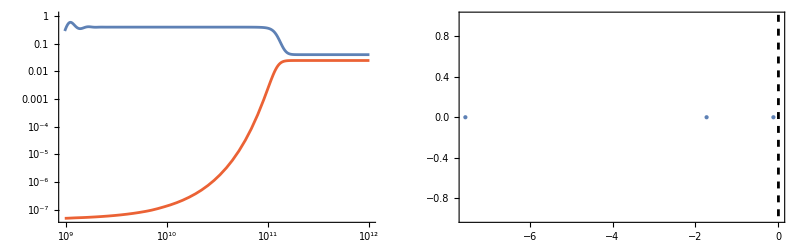

```mathematica
ndeqns=PCRSim[eqnP,eqnC,eqnR,0];
tmax = 10^12;
PredMass = 10^5;
PercentGrowthConsumer=0.8; (*Percent with which the predator relies on Consumer 1 for food*)
PercentSubsidy =0.02;
sol = NDSolve[{
ndeqns/.{Mp->PredMass,w->PercentGrowthConsumer,ϵ->PercentSubsidy}},
{P,C1,R},{t,tmax},Method->Automatic];
{Psol,Csol}/.{Mp->PredMass,w->PercentGrowthConsumer,ϵ->PercentSubsidy}
Eigs=Eigenvalues[JacobianFullModel/.{Mp->PredMass,w->PercentGrowthConsumer,ϵ->PercentSubsidy}];
Re[Eigs]
GraphicsRow[{
LogLogPlot[Evaluate[{P[t],C1[t]}/.sol],{t,0,tmax},PlotStyle->{ColorData[97,4],ColorData[97,1]}],
Show[{ListPlot[Transpose[{Re[Eigs],Im[Eigs]}],Frame->True,PlotStyle->PointSize[Large]],ListPlot[{{0,-10},{0,10}},Joined->True,PlotStyle->Directive[{Black,Dashed}]]}]
}]
```

```mathematica
wvalues = Table[i,{i,0.01,1,0.01}];
epsilonvalues = Table[10^i,{i,-3,0,0.005}];
CsolMass = ((1/OptPreyMass[Mp])*Csol)/.Mp->Mass;
PsolMass = ((1/Mp)*Psol)/.{Mp->Mass};
```

```mathematica
ThresholdsOverWEpsilonAlternate=Flatten[ParallelTable[
{thresholdsizeC,existC}= DetectThresholdSol[CsolMass/.{w->wvalues[[i]],ϵ->epsilonvalues[[j]]}];
{thresholdsizeP,existP} = DetectThresholdSol[PsolMass/.{w->wvalues[[i]],ϵ->epsilonvalues[[j]]}];
{wvalues[[i]],epsilonvalues[[j]],thresholdsizeC,thresholdsizeP, existC,existP},
{i,1,Length[wvalues]},{j,1,Length[epsilonvalues]}],1];
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/data/thresholdsoverwepsilon.csv"}],ThresholdsOverWEpsilonAlternate,"CSV"]*)
```

```mathematica
ThresholdsOverWEpsilonAlternateOrig=Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/data/thresholdsoverwepsilon.csv"}]];
```

08/15/24
Reverse the w_1 axis to be w_S = 1 - w_1

```mathematica
ThresholdsOverWEpsilonAlternate = ThresholdsOverWEpsilonAlternateOrig;
ThresholdsOverWEpsilonAlternate[[All,1]] = 1- ThresholdsOverWEpsilonAlternate[[All,1]]; (*Change w1 to wS = 1 - w1*)
```

```mathematica
PreyThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],OptPreyMass[ThresholdsOverWEpsilonAlternate[[All,3]]]}];
PredThresholdMatrixAlternate = Transpose[{ThresholdsOverWEpsilonAlternate[[All,1]],ThresholdsOverWEpsilonAlternate[[All,2]],ThresholdsOverWEpsilonAlternate[[All,4]]}];

PreySizeGapPosAlternate=Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#>5000&&#<25000&)],1];
PredSizeGapPosAlternate=Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>5000&&#<25000&)],1];
PreyTMAlternate=PreyThresholdMatrixAlternate[[PreySizeGapPosAlternate,1;;2]];
PredTMAlternate=PredThresholdMatrixAlternate[[PredSizeGapPosAlternate,1;;2]];
MissingPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosC]][[All,2]]}];
MissingPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,4]],_?(#==Missing[]&)],1];
MissingPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[MissingPosP]][[All,2]]}];

UpperThreshold = 10^6.2;
LowerThreshold = 10;
UpperThresholdPosP = Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#>UpperThreshold||#<LowerThreshold&)],1];
PredThresholdMatrixAlternate[[UpperThresholdPosP,3]]=Missing[];
PredUpperThreshold=PredThresholdMatrixAlternate[[UpperThresholdPosP,1;;2]];

(*ExtinctPosC1 = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtinctPosC2= Flatten[Position[PreyThresholdMatrixAlternate[[All,3]],_?(#>10&)],1];
ExtinctPos = Flatten[Intersection[{ExtinctPosC1,ExtinctPosC2}],1];*)
ExtinctPosC1 = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#==0&)],1];
ExtinctPosC2= Flatten[Position[PreyThresholdMatrixAlternate[[All,3]],_?(#<1&&#>0.0&)],1];
ExtinctPosC=Flatten[Union[{ExtinctPosC1,ExtinctPosC2}],1];
(*ExtantPosC = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,5]],_?(#>0&)],1];*)
ExtinctPointsC = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosC]][[All,2]]}];
ExtinctPosP = Flatten[Position[ThresholdsOverWEpsilonAlternate[[All,6]],_?(#==0&)],1];
ExtinctPointsP = Transpose[{ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,1]],ThresholdsOverWEpsilonAlternate[[ExtinctPosP]][[All,2]]}];
```

```mathematica
ThresholdPlotAlternate=GraphicsRow[{
Show[{
ListContourPlot[PredThresholdMatrixAlternate,FrameLabel->{"Prop. growth from subsidy w_S","Subsidy availability S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},{1,All}},ContourStyle->None,ColorFunction->"SiennaTones",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"M_P^†",LabelStyle->{Italic,(*FontFamily->"Times New Roman",*)FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16,Black]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
(*Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTMAlternate[[All,1]],Log@PredTMAlternate[[All,2]]}]]}],*)
(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsP[[All,1]],Log@MissingPointsP[[All,2]]}],0.02,All]}]*)
Graphics[{White,ConcaveHullMesh[Transpose[{PredUpperThreshold[[All,1]],Log@PredUpperThreshold[[All,2]]}],0.02,All]}],
(*Note that Sint = 0.08 corresponds to an M_P threshold of 12 grams*)
(*LogPlot[Sint/(1-w)/.Sint->0.173(*0.08*),{w,0,1},PlotStyle->Directive[{Thickness[0.03],Dashed,Gray}]],*)
LogPlot[Sint/(1-(1-w))/.Sint->0.08,{w,0,1},PlotStyle->Directive[{Thickness[0.03],Dashed,Black}]]
}],
Show[{
ListContourPlot[PreyThresholdMatrixAlternate,FrameLabel->{"Prop. growth from subsidy w_S","Subsidy availability S (g·m^-2)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotRange->{{0,1},{0.001,1},{0.1,All}},ContourStyle->None,ColorFunction->"StarryNightColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"M_C^‡",LabelStyle->{Italic,(*FontFamily->"Times New Roman",*)FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16,Black]]
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
(*Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTMAlternate[[All,1]],Log@PreyTMAlternate[[All,2]]}]]}],*)
(*Graphics[{White,Opacity[1],ConcaveHullMesh[Transpose[{MissingPointsC[[All,1]],Log@MissingPointsC[[All,2]]}],0.02,All]}],*)

(*,Graphics[{Gray,ConcaveHullMesh[Transpose[{ExtinctPointsC[[All,1]],Log@ExtinctPointsC[[All,2]]}],0.02,All]}]*)
,Graphics[{Gray,ConcaveHullMesh[Transpose[{PredUpperThreshold[[All,1]],Log@PredUpperThreshold[[All,2]]}],0.02,All]}]
}]
},ImageSize->850,Spacings->0]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/final_figures/fig_thresholdsoverwepsilon.png"}],ThresholdPlotAlternate,"PNG"]
```

/Users/justinyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/final_figures/fig_thresholdsoverwepsilon.png

```mathematica
"/Users/jdyeakel/Dropbox/PostDoc/2024_PCR/figures/fig_thresholdsoverwepsilon.png"
```

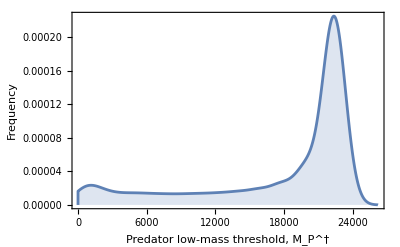

32499.1

{17756.5,10788.9,24724.2}

6967.64

```mathematica
SmallSizedThresholdPos = Flatten[Position[PredThresholdMatrixAlternate[[All,3]],_?(#<UpperThreshold&)],1];
PredThresholdSizes=PredThresholdMatrixAlternate[[SmallSizedThresholdPos,3]];
SpecialistPredThresholdPos = Flatten[Position[PredThresholdMatrixAlternate[[All,1]],_?(#>0.95&)],1];
SpecialistPredThresholdSizes = PredThresholdMatrixAlternate[[Intersection[SmallSizedThresholdPos,SpecialistPredThresholdPos],3]];
PredThresholdHistPlot = SmoothHistogram[SpecialistPredThresholdSizes,1000,Frame->True,FrameLabel->{"Predator low-mass threshold, M_P^†","Frequency"},PlotRange->{{0,All},All},Filling->Bottom]
Mean[PredThresholdSizes]
{Mean[SpecialistPredThresholdSizes],Mean[SpecialistPredThresholdSizes]-StandardDeviation[SpecialistPredThresholdSizes],Mean[SpecialistPredThresholdSizes]+StandardDeviation[SpecialistPredThresholdSizes]}
StandardDeviation[SpecialistPredThresholdSizes]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/figures/fig_predthresholdhist.pdf"}],PredThresholdHistPlot,"PDF"]
```

```mathematica
"/Users/jdyeakel/Dropbox/PostDoc/2024_PCR/figures/fig_predthresholdhist.pdf"
```

Mode of the distribution ^^ is roughly 22 Kg - this should be the focus in terms of results, rather than the average (which is in a frequency valley)

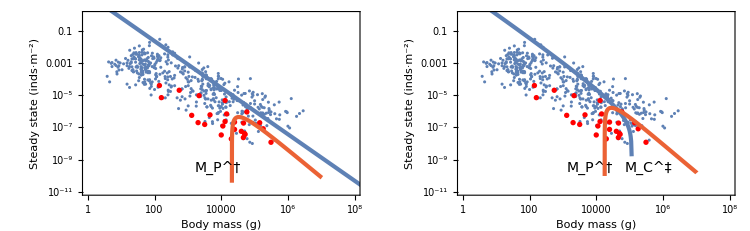

```mathematica
PercentGrowthConsumer=1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.08;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
ThresholdPopulationPlotNoSubPredSpace=
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16,Black]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->14],{Log@(10^3.9),Log@(10^(-9.5))}]}](*,
Graphics[{Text["M_C^‡",{Log@(10^7),Log@(10^(-9))}]}]*)
(*LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]*)
},ImageSize->300];
PercentGrowthConsumer=0.5; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.01;
ConsDensityList=Table[{10^i,((1/OptPreyMass[Mp])*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue})/.Mp->10^i},{i,1,8,0.01}];
ConsDensityListConsMass = Transpose[{OptPreyMass[ ConsDensityList[[All,1]]],ConsDensityList[[All,2]]}];
ThresholdPopulationPlotSubPredSpace=
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16,Black]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],*)
ListLogLogPlot[ConsDensityListConsMass,Joined->True,PlotStyle->{Thickness[0.01],ColorData[97,1]}],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,1,10^8},Frame->True,PlotStyle->{Thickness[0.01],ColorData[97,4]}],
Graphics[{Text[Style["M_P^†",FontSize->14],{Log@(10^3.8),Log@(10^(-9.5))}]}],
Graphics[{Text[Style["M_C^‡",FontSize->14],{Log@(10^5.55),Log@(10^(-9.5))}]}]
(*LogLogPlot[(1/OptPreyMass[Mp])*PreyDensityTheoreticalMax[OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/Mp)*PredatorDensityTheoreticalMax[Mp,OptPreyMass[Mp]]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{Mp,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]*)
},ImageSize->300];
ThresholdPopulationPlotCombPredSpace=GraphicsRow[{ThresholdPopulationPlotNoSubPredSpace,ThresholdPopulationPlotSubPredSpace},ImageSize->750,Spacings->0]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/final_figures/fig_thresholdspopcomb_predpersp.pdf"}],ThresholdPopulationPlotCombPredSpace,"PDF"]
```

```mathematica
"/Users/jdyeakel/Dropbox/PostDoc/2024_PCR/figures/fig_thresholdspopcomb_predpersp.pdf"
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/final_figures/fig_thresholdspopcomb_predpersp.png"}],ThresholdPopulationPlotCombPredSpace,"PNG"]
```

/Users/justinyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/final_figures/fig_thresholdspopcomb_predpersp.png

```mathematica
"/Users/jdyeakel/Dropbox/PostDoc/2024_PCR/figures/fig_thresholdspopcomb_predpersp.png"
```

```mathematica
CombinedSubsidyFig = GraphicsColumn[{ThresholdPopulationPlotCombPredSpace,ThresholdPlotAlternate},ImageSize->1000,Spacings->-40]
```

-Graphics-